# 1-D universal estimator using CNN

## Generating data (without duplicating θ and logging the histogram)

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for a given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, f_, range_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS},
		params=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
		(*generate M different random initparameters in the range [min_θ,max_θ]*) 
		samples=Table[f[params[[i]],n],{i,1,M}];
		(*generate M distributions, each distribution has n number/data*, now we have M*n data*)
		MAXBINS=1000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=HistogramList[x,{0,nbins,1}][[2]]; (*without using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[5,10,f,{2,3}]//TableForm];*)
```

{8,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.28381
{5,3,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}→2.29096
{7,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.3542
{8,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.35051
{8,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1}→2.77108

## CNN (using the model in the report)

Generate a DNN for predicting the parameter θ from the distribution histogram
The input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
ReshapeLayer[{1,bins}],  (*change the vector to 1d matrix for convolution*)
ConvolutionLayer[32,{3}], (*32 filters, kernel size 3*)
ElementwiseLayer[Ramp], (*relu activation*)
PoolingLayer[{2},"Function"->Max],  (*max pooling size 2*)
FlattenLayer[],
LinearLayer[{64}], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], (*relu activation*)
LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using CNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 1024;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->256
 (*LearningRate->0.001 learning rate*)
 (*LossFunction->MeanSquaredLossLayer[] loss: mse*)
];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with DNN

M: The number of different θ generated in the range [min_θ, max_θ]
S: The number of duplication of θ 
n: The number of samples drawn for a given θ

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, initΘ, expansion,S},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];
(*define the size of the test set*)
M = 20;
S = 5；
n = 1024;

initΘ=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
(*generate M different random initΘ in the range [min_θ,max_θ]*)
expansion[j_]:=Table[initΘ[[j]],S]; 
(*define an expansion function for duplicating the initΘ*)
Θ=Flatten[Table[expansion[w],{w,1,M}]];
(*increase the number of each different parameters to S, now we have M*S Θ *)		
g[θ_,a_] := RandomVariate[dist[θ],a];
(*create M*S test samples*)
samples = Table[g[Θ[[i]], n], {i,1,M*S,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M*S,1 }];

(*evaluate prediction errors*)

e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M*S,1 }];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["RMSE:",RootMeanSquare[e]];

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for the different distributions

### Yule-Simon distribution

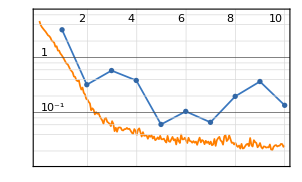
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:400  rounds:10  time:52s  examples/s:1997
data | ,,  training examples:10000  validation examples:5000  processed examples:102400  skipped examples:0
method | ,,  ADAMoptimizer  batch size256CPU
round | ,,  loss:2.41×10^-2
validation | ,,  loss:1.35×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.30884,2.30884,2.30884,2.30884,2.30884,2.64072,2.64072,2.64072,2.64072,2.64072,2.61495,2.61495,2.61495,2.61495,2.61495,2.90985,2.90985,2.90985,2.90985,2.90985,2.23009,2.23009,2.23009,2.23009,2.23009,2.37367,2.37367,2.37367,2.37367,2.37367,2.50778,2.50778,2.50778,2.50778,2.50778,2.7603,2.7603,2.7603,2.7603,2.7603,2.06322,2.06322,2.06322,2.06322,2.06322,2.92914,2.92914,2.92914,2.92914,2.92914,2.60526,2.60526,2.60526,2.60526,2.60526,2.35142,2.35142,2.35142,2.35142,2.35142,2.83802,2.83802,2.83802,2.83802,2.83802,2.66756,2.66756,2.66756,2.66756,2.66756,2.45515,2.45515,2.45515,2.45515,2.45515,2.35905,2.35905,2.35905,2.35905,2.35905,2.2189,2.2189,2.2189,2.2189,2.2189,2.3517,2.3517,2.3517,2.3517,2.3517,2.3376,2.3376,2.3376,2.3376,2.3376,2.36808,2.36808,2.36808,2.36808,2.36808}

θ̂: {2.70027,2.44365,2.52695,2.64888,2.26304,2.64033,2.92002,2.89805,2.27562,2.98493,2.47149,2.16214,2.79547,2.87731,2.83346,2.7482,2.72934,2.89108,3.1085,3.2715,2.36083,2.45429,2.61815,2.22511,2.00502,2.55178,2.80115,2.33206,2.9143,2.76911,2.40128,2.38555,2.33362,2.53641,2.46518,2.49441,2.86866,2.94971,2.98328,2.65938,2.51703,2.38264,2.19466,2.55051,1.88188,2.76606,2.8166,2.78693,2.62537,2.61152,2.8617,2.66396,2.71153,2.89932,2.91703,2.67279,2.57477,2.57644,2.6379,2.28564,3.0696,2.98524,2.83134,2.51494,2.92535,2.79766,2.6751,2.59908,2.63774,2.51272,2.71573,2.4033,2.66022,2.63223,2.25248,2.58487,2.3759,2.46537,2.79243,2.3938,2.29594,2.29066,2.67821,2.50272,2.61291,2.38296,2.49795,2.82342,1.97896,2.70052,2.17673,2.41248,2.56194,2.12775,2.44967,2.03904,2.29338,2.36712,2.58668,2.71905}

abs(θ-θ̂): {0.391433,0.134818,0.218119,0.340049,0.0457907,0.000390686,0.279306,0.257328,0.365097,0.344209,0.143461,0.452812,0.180516,0.262354,0.218503,0.161641,0.180505,0.0187625,0.198651,0.361652,0.130737,0.224203,0.388059,0.00497432,0.225069,0.178105,0.427474,0.0416149,0.540625,0.395438,0.106496,0.122224,0.174152,0.0286368,0.0425979,0.265889,0.108355,0.189405,0.222975,0.100925,0.453812,0.319418,0.131446,0.487295,0.18134,0.16308,0.11254,0.142204,0.303764,0.317614,0.256443,0.0587086,0.10627,0.294069,0.311777,0.321374,0.223347,0.225023,0.286477,0.065776,0.231576,0.147217,0.00667956,0.323082,0.087332,0.130096,0.00753446,0.068482,0.0298205,0.154847,0.260581,0.051856,0.205066,0.177076,0.202674,0.22582,0.0168529,0.106323,0.433377,0.0347526,0.0770376,0.0717583,0.459306,0.283823,0.39401,0.0312576,0.146242,0.47172,0.372743,0.348821,0.160873,0.0748786,0.224334,0.209856,0.112064,0.32904,0.0746998,0.000966666,0.218595,0.350962}

RMSE:0.244284

```mathematica
{Θ, e} = RunExperiment[WaringYuleDistribution, {2,3}];
```

### Poisson distribution

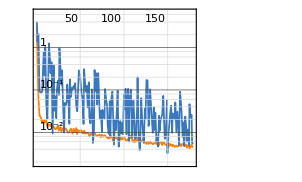
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:7160  rounds:179  time:39s  examples/s:47789
data | ,,  training examples:10000  validation examples:5000  processed examples:1832960  skipped examples:0
method | ,,  ADAMoptimizer  batch size256CPU
round | ,,  loss:4.44×10^-3
validation | ,,  loss:5.32×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.01509,2.01509,2.01509,2.01509,2.01509,2.90892,2.90892,2.90892,2.90892,2.90892,2.7291,2.7291,2.7291,2.7291,2.7291,2.94594,2.94594,2.94594,2.94594,2.94594,2.30715,2.30715,2.30715,2.30715,2.30715,2.56908,2.56908,2.56908,2.56908,2.56908,2.10747,2.10747,2.10747,2.10747,2.10747,2.47113,2.47113,2.47113,2.47113,2.47113,2.53112,2.53112,2.53112,2.53112,2.53112,2.42805,2.42805,2.42805,2.42805,2.42805,2.15909,2.15909,2.15909,2.15909,2.15909,2.62015,2.62015,2.62015,2.62015,2.62015,2.62893,2.62893,2.62893,2.62893,2.62893,2.08111,2.08111,2.08111,2.08111,2.08111,2.29229,2.29229,2.29229,2.29229,2.29229,2.97727,2.97727,2.97727,2.97727,2.97727,2.11694,2.11694,2.11694,2.11694,2.11694,2.81626,2.81626,2.81626,2.81626,2.81626,2.78062,2.78062,2.78062,2.78062,2.78062,2.81876,2.81876,2.81876,2.81876,2.81876}

θ̂: {2.00605,2.02094,2.0154,1.96062,2.0698,2.86399,2.83994,2.82096,2.85523,2.82406,2.68507,2.65622,2.73511,2.70826,2.74003,2.91302,2.88121,2.97474,2.84423,2.93469,2.32588,2.27032,2.23505,2.24517,2.36525,2.53763,2.45288,2.49431,2.50856,2.55912,2.11078,2.07365,2.01944,2.15801,2.10874,2.50504,2.51852,2.48694,2.44688,2.38562,2.59893,2.43876,2.63709,2.54165,2.47893,2.42752,2.5629,2.47126,2.34451,2.40472,2.17124,2.17883,2.1096,2.1288,2.19616,2.58758,2.61104,2.61015,2.60388,2.64425,2.55834,2.6601,2.58756,2.69492,2.66935,2.08092,2.08671,2.10405,2.08192,2.13097,2.30489,2.36866,2.31451,2.31635,2.38342,2.87348,2.93228,2.8474,2.88952,2.8626,2.05279,2.05293,2.27406,2.09375,2.08626,2.82924,2.85398,2.76389,2.86447,2.85834,2.68415,2.73598,2.78216,2.74427,2.82992,2.78111,2.82069,2.785,2.86492,2.79959}

abs(θ-θ̂): {0.00904114,0.00584572,0.000307015,0.0544762,0.0547046,0.0449334,0.0689855,0.0879594,0.0536972,0.0848599,0.0440294,0.072879,0.00601731,0.0208384,0.0109371,0.032924,0.0647333,0.0288002,0.101708,0.0112482,0.0187252,0.0368326,0.0721016,0.0619764,0.0581024,0.031458,0.116207,0.0747753,0.0605274,0.00996502,0.00331256,0.0338216,0.0880261,0.050544,0.00126978,0.0339118,0.0473884,0.0158051,0.0242506,0.085512,0.0678136,0.0923634,0.105968,0.0105276,0.0521901,0.000532848,0.134853,0.0432129,0.0835395,0.0233328,0.0121517,0.0197411,0.0494885,0.0302896,0.0370655,0.0325714,0.00910931,0.0100005,0.016274,0.0240943,0.0705882,0.0311793,0.0413691,0.0659972,0.0404257,0.000196017,0.00560042,0.0229334,0.000807725,0.049859,0.0125923,0.0763657,0.0222197,0.02406,0.0911291,0.103788,0.0449837,0.129869,0.0877497,0.114663,0.0641523,0.0640107,0.157121,0.0231906,0.0306855,0.0129863,0.0377258,0.052363,0.048215,0.0420793,0.0964699,0.0446396,0.00154396,0.0363491,0.0492978,0.0376542,0.00193091,0.0337611,0.0461545,0.0191727}

RMSE:0.0568948

```mathematica
{Θ, e} = RunExperiment[PoissonDistribution, {2,3}];
```

### Geometric distribution

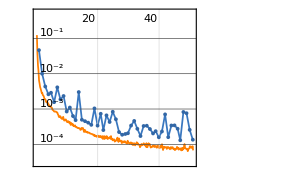
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2040  rounds:51  time:33s  examples/s:15890
data | ,,  training examples:10000  validation examples:5000  processed examples:522240  skipped examples:0
method | ,,  ADAMoptimizer  batch size256CPU
round | ,,  loss:8.22×10^-5
validation | ,,  loss:1.35×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {0.243636,0.243636,0.243636,0.243636,0.243636,0.246766,0.246766,0.246766,0.246766,0.246766,0.258911,0.258911,0.258911,0.258911,0.258911,0.26119,0.26119,0.26119,0.26119,0.26119,0.231879,0.231879,0.231879,0.231879,0.231879,0.243934,0.243934,0.243934,0.243934,0.243934,0.272958,0.272958,0.272958,0.272958,0.272958,0.285963,0.285963,0.285963,0.285963,0.285963,0.210278,0.210278,0.210278,0.210278,0.210278,0.237271,0.237271,0.237271,0.237271,0.237271,0.250087,0.250087,0.250087,0.250087,0.250087,0.212962,0.212962,0.212962,0.212962,0.212962,0.229212,0.229212,0.229212,0.229212,0.229212,0.282629,0.282629,0.282629,0.282629,0.282629,0.261014,0.261014,0.261014,0.261014,0.261014,0.253309,0.253309,0.253309,0.253309,0.253309,0.237435,0.237435,0.237435,0.237435,0.237435,0.202276,0.202276,0.202276,0.202276,0.202276,0.287194,0.287194,0.287194,0.287194,0.287194,0.22399,0.22399,0.22399,0.22399,0.22399}

θ̂: {0.214879,0.225748,0.243043,0.254681,0.262443,0.241804,0.254784,0.24783,0.235009,0.282771,0.25549,0.259797,0.252853,0.264611,0.264584,0.278204,0.253549,0.264953,0.277238,0.259544,0.247293,0.224104,0.234894,0.250342,0.234035,0.233022,0.262316,0.251038,0.233579,0.245065,0.272432,0.269325,0.253723,0.258728,0.293194,0.271445,0.280915,0.279652,0.283112,0.285381,0.210481,0.218648,0.212272,0.206105,0.211217,0.232337,0.236287,0.243359,0.2725,0.232438,0.293511,0.247028,0.238814,0.254402,0.234288,0.225849,0.189546,0.202686,0.21169,0.219684,0.22187,0.236464,0.235852,0.228123,0.232732,0.273653,0.288233,0.281023,0.284322,0.290304,0.25199,0.262646,0.279229,0.26336,0.262714,0.244529,0.2506,0.23694,0.259085,0.260256,0.250666,0.236805,0.227054,0.239579,0.262649,0.207719,0.204615,0.208846,0.203945,0.202438,0.284457,0.266125,0.289561,0.289606,0.292781,0.225621,0.226908,0.232487,0.223321,0.225936}

abs(θ-θ̂): {0.0287568,0.0178873,0.000592108,0.0110453,0.0188071,0.00496231,0.00801734,0.00106398,0.0117568,0.0360044,0.00342159,0.000885771,0.00605808,0.00570013,0.00567259,0.0170137,0.00764141,0.0037634,0.0160479,0.00164593,0.0154138,0.00777516,0.00301477,0.0184628,0.00215599,0.0109116,0.0183818,0.00710426,0.0103544,0.00113155,0.000525347,0.00363292,0.0192349,0.0142295,0.0202366,0.0145183,0.00504796,0.00631134,0.00285075,0.00058238,0.000202786,0.00836967,0.00199392,0.00417351,0.000938635,0.00493328,0.000983608,0.00608851,0.0352294,0.00483231,0.043424,0.00305908,0.0112731,0.00431452,0.0157994,0.0128871,0.023416,0.0102752,0.00127153,0.00672216,0.00734197,0.00725215,0.00663939,0.00108921,0.00351977,0.00897568,0.00560391,0.0016058,0.00169305,0.00767464,0.00902324,0.0016321,0.0182154,0.0023464,0.00170026,0.00878078,0.00270963,0.0163693,0.00577551,0.00694665,0.0132316,0.000629413,0.0103811,0.0021442,0.0252142,0.00544324,0.00233841,0.00656971,0.00166875,0.000161763,0.00273674,0.0210686,0.00236718,0.00241185,0.0055869,0.00163185,0.00291854,0.00849753,0.000668052,0.00194636}

RMSE:0.0117446

```mathematica
{Θ, e} = RunExperiment[GeometricDistribution, {0.2,0.3}];
```